# Report Project 2

Course code: IX1500 - Discrete Mathematics
Date: 2017-10-03

Evan Saboo, saboo@kth.se
Xing Guan, xguan@kth.se

Task 1a: RSA cipher

## Summary

### Task

Alice sent an RSA encrypted message to Bob by using her own private key and Bobs public key to encrypt the message. 
Our task is to solve Bobs problem by using Bobs private key and Alice public key to decrypt the cipher message. 
The only information we got from Bob is his public key (n_Bob,e_Bob), Alice public key (n_Alice,e_Alice) and the cipher message:

n_Alice = 14625052655936968690439555839903578410656653152402266773966305647313
e_Alice = 9103

n_Bob = 891257371165353198597686733461449215081540410212576138836198818353
e_Bob = 6389

cipher={4430210573981968733755487447818174029880701596884938356564639003222,2851153559114750987221731555966122250132614620940651980091426872783,7706806242317911603638504323916964668918097951180075641184510131492,3684227409638269668959612918228029487936911649602484180495870360134,118390233898339944208891887229177617429671446231727377499079969939,11722755771961643408261179942790037153532726213028762901063706465880,13859812858423457720552211210177480158021647193707898449643563546715,8458200553283608142592103589289032864817455387331640007234518389001,4203062251335458332458951560795586742826858693125368654700629553235,11246017592897572378455633552556960091533916541949272900160606355164,528729157482321024630053104368111400799635858352035984875544277541,14149609332514930578966644135292557372570883055216115495760639164502,6806693065526086081574819023329054541636484663342321332752294055806,10173212145631688548727430811241580523813551542356631310237779750220,6759760040422316973322423168431166905944837651248859901210533615722,11488644301666039406597033276777701689096765993957684011886918061630,10421162414768710251337302689028405059375889881305351342596162625647,9496359638348947223087997149242581766202717301485526573539185466328,6021527813042783330194131859432644092333420618174656828129608651886,1862712526928231860818857411345402991522792361353775067366437910859,5770870235309404532139302393417410250573907045700501009827409811147,7754796273877044686482387739917927617087893337176831108280229804774,1689445149306311402232833597026076887079752228378923964144759423086,1448530945006829418385610770415140752515002298435493622427431846992,7445869507503892181715468267483205548161014207123217105479157092169,10975830923316626122520530596740793665823967057824410678091427215458,9807539864876132360289770201821020858873102738795986884424480971219};

### Result

By using Bobs public key (n_Bob,e_Bob) and Alice public key (n_Alice,e_Alice), we were able to decrypt the cipher message sent from Alice to Bob:

Congratulations! You have now managed to crack the RSA cipher. Your task is as follows: write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the Swedish text DISKRET MATTE, DE E FETT NAIS! for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits with your computer.

And the reason why the numbers in the cipher list are of the same size is because the probability of getting the size 68 or 67 is approx.  93% while getting a size smaller than 67 is ~7%. In other words, the probability is higher if we get a size closer or equal to n_Alice.

## RSA authentication and decryption

### Decrypting the cipher message

Alice used RSA to Authenticate the message.
We know that Alice used her own secret key d_Alice to encrypt the message because Bob wanted to be assured that the message was sent from Alice. 

Alice encrypted the message by taking min(n_Alice,n_Bob) and applied into the formula below: 

n_Bob<n_Alice⇒c_0≡_n_Bob m_Alice^e_Bob ⇒

c_Alice≡_n_Alice c_0^d_Alice

But the message was bigger than min(n_Alice,n_Bob) and she had to divide the message into several subtext before the encryption process, where every subtext is smaller than min(n_Alice,n_Bob).


To decrypt the message, we start by using the public key, which belongs to max(n_Alice,n_Bob) in the formula below:

n_Alice>n_Bob⇒c_1≡_n_Alice c_Alice^e_Alice⇒

m_Alice≡_n_Bob c_1^d_Bob

We need four components to decrypt the cipher message:

n_Alice = 14625052655936968690439555839903578410656653152402266773966305647313

e_Alice = 9103

n_Bob= 891257371165353198597686733461449215081540410212576138836198818353

d_Bob = ?

To calculate d_Bob we first need to factor out two distinct prime numbers (p, q) from n_Bob and  calculate ϕ_Bob :

p = 457792861431456494922119050690577  
q = 1946857293446017662241143108141089
 
ϕ_Bob = (p -1) * (q -1)
ϕ_Bob = 891257371165353198597686733461446810431385532738418975574039986688
 
The last step is to use Euler’s Totient Theorem to calculate d_Bob:
d_Bob ≡_n_Bob e^-1→  
d_Bob≡_n_Bob 6389^-1 
d_Bob= 67796381653836540071760174121499945197942302224271657869617065821  

The reason why we want Bobs decryption key is because Alice used Bobs public key to encrypt the message and we know that Bobs decryption key can “cancel out” the encryption key:

e d≡_ϕ 1
m_Alice≡_n_Bob m_Alice^(e_Bob* d_Bob) 

Now we can begin calculating c_1by decrypting the cipher message with Alice public key.

c_1≡_n_Alice c_Alice^e_Alice → 

c_1≡_n_Alice cipher^6389  

The last step is to decrypt c_1with Bobs private key to get Alice message in plain text.

m_Alice≡_n_Alice c_1^d_Bob →

m_Alice≡
"Congratulations! You have now managed to crack the RSA cipher. Your task is as follows: write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the Swedish text DISKRET MATTE, DE E FETT NAIS! for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits with your computer."

We had to decrypt every cipher message individually in the cipher list and join all subtexts together to get the final message.

### Why are the numbers in the cipher list the same size?

When Alice used modulo n_Alice to get the cipher message we knew that value can only be between  0≤c≤ (n_Alice-1).
We can predict the probability of getting a certain size S
by counting all occurrences of S and divide it by (n_Alice -1):

Probability of getting size S=(|S|)/(n_Alice-1)

Lets begin with the probability of getting  S = 68 and 67, which are the two highest sizes we can get from n_Alice:

 P(68) = ((n_Alice) - (10^67 - 1))/n_Alice
 P(68) ≈ 0.3162  = 31.62%

P(67) = ((10^67- 1) - (10^66 - 1))/n_Alice
 P(67) ≈ 0.6154  = 61.54%
 
 We can conclude that the probability of getting size 68 or 67 is approx.  93% while getting S<67 is ~7%.
 
 If we calculate the probability of getting S=66 and S=65 we get:

  P(66) = ((10^66-1) - (10^65 - 1))/n_Alice
 P(66) ≈ 0.0615  = 6.15%

P(65) = ((10^65- 1) - (10^64 - 1))/n_Alice
 P(65) ≈ 0.0062  = 0.62%

We can also conclude that for every time the size S decreases by 1 the probability gets 10 times smaller (if S≥ 67).

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
nAlice=14625052655936968690439555839903578410656653152402266773966305647313;
eAlice=9103;
```

```mathematica
nBob=891257371165353198597686733461449215081540410212576138836198818353;
eBob=6389;
```

```mathematica
cipher={4430210573981968733755487447818174029880701596884938356564639003222,2851153559114750987221731555966122250132614620940651980091426872783,7706806242317911603638504323916964668918097951180075641184510131492,3684227409638269668959612918228029487936911649602484180495870360134,118390233898339944208891887229177617429671446231727377499079969939,11722755771961643408261179942790037153532726213028762901063706465880,13859812858423457720552211210177480158021647193707898449643563546715,8458200553283608142592103589289032864817455387331640007234518389001,4203062251335458332458951560795586742826858693125368654700629553235,11246017592897572378455633552556960091533916541949272900160606355164,528729157482321024630053104368111400799635858352035984875544277541,14149609332514930578966644135292557372570883055216115495760639164502,6806693065526086081574819023329054541636484663342321332752294055806,10173212145631688548727430811241580523813551542356631310237779750220,6759760040422316973322423168431166905944837651248859901210533615722,11488644301666039406597033276777701689096765993957684011886918061630,10421162414768710251337302689028405059375889881305351342596162625647,9496359638348947223087997149242581766202717301485526573539185466328,6021527813042783330194131859432644092333420618174656828129608651886,1862712526928231860818857411345402991522792361353775067366437910859,5770870235309404532139302393417410250573907045700501009827409811147,7754796273877044686482387739917927617087893337176831108280229804774,1689445149306311402232833597026076887079752228378923964144759423086,1448530945006829418385610770415140752515002298435493622427431846992,7445869507503892181715468267483205548161014207123217105479157092169,10975830923316626122520530596740793665823967057824410678091427215458,9807539864876132360289770201821020858873102738795986884424480971219};
```

First we factor out two prime numbers (p,q) from n_Bob.

```mathematica
{{pBob,p},{qBob,q}} =FactorInteger[nBob]
```

{{457792861431456494922119050690577,1},{1946857293446017662241143108141089,1}}

We subtract 1 from p and q, and multiply both with each other to get  ϕ_Bob.

```mathematica
ϕBob=(pBob-1)(qBob-1)
```

891257371165353198597686733461446810431385532738418975574039986688

Now we can use Euler’s Totient Theorem to calculate the inverse of e_Bob, which is the decryption key d_Bob.

```mathematica
dBob=PowerMod[eBob,-1,ϕBob]
```

67796381653836540071760174121499945197942302224271657869617065821

Next we follow the steps described in the previous section, by decrypting every cipher message in the cipher list with e_Alice to “cancel out” d_Alice.

```mathematica
For[i = 1, i < Length[cipher] +1, i++, 
cipher[[i]] = PowerMod[cipher[[i]],eAlice,nAlice]
]
```

Now we can use d_Bob to decrypt the cipher list because we now that the cipher message was encrypted twice, first by e_Bob and later by d_Alice.

```mathematica
For[i = 1, i < Length[cipher] +1, i++, 
cipher[[i]] = PowerMod[cipher[[i]], dBob, nBob]

]
```

```mathematica
crackedMsg = cipher;
```

```mathematica
B= 256;
```

The last step is to decode the decrypted message list from base 256 to ascii characters.

```mathematica
For[i = 1, i < Length[cipher]+1, i++, 
q=cipher[[i]];ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B]
];
crackedMsg[[i]] =FromCharacterCode[ascii];
]
```

We now have the message which Bob wanted in clear text.

```mathematica
StringJoin[crackedMsg]
```

Congratulations! You have now managed to crack the RSA cipher. Your task is as follows: write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. When you are finished with your method, you should investigate how long it will take to crack the cipher of the Swedish text DISKRET MATTE, DE E FETT NAIS! for different sizes on your public key n (100-200 bits). Visualize your results in a proper graph. It is very important that you study the section 2.3 in the instructions. Your graph should lead you to a model where you can predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits with your computer.

Task 1b: Prediction and selection of mathematical model

## Summary

### Task

Write a method RSAcrack[cipher,n,e] that will crack a standard RSA cipher and delivers clear text from the string cipher. Also using the function and other functions we gonna investigate how long it will take to crack the cipher of the Swedish text DISKRET MATTE, DE E FETT NAIS! for different sizes on our public key n (100-200 bits). Visualize the results in a proper graph. The created graph should predict how long it would take to crack a cipher if n is 1024, 2048 bits or 4096 bits with our computer.

### Result

Using the formula m_Alice≡_n_Bob c_Alice^d_Bob and given c_Alice and n_Bob we could calculate decryption key, d_Bob which is implemented in the method RSAcrack[cipher, n, e]. For more detail, see the explanation under subsection “RSAcrack method”.

The exponential function is used to our model. Using the graph which was created, we could find our mathematical model to calculate the time it takes to crack the cipher if  n is 1024, 2048 bits or 4096 bits with our computer. The answer is presented in the table below.

Size,bit | Time,year
1024 | 7.271*10^23
2048 | 4.076*10^60
4096 | 1.282*10^134

## The selected model and size of the cipher

### RSAcrack method

RSAcrack method use the formula m_Alice≡_n_Bob c_Alice^d_Bob to crack the cipher. Given the  c_Alice and n_Bob we need to find out d_Bob.

In order to do find d_Bob we use the Mathematica function, FactorInteger[n] to break down the n to two primes where n is the multiplication of two large primes and is public number from the person where the message is sent to. In this case it is Bob the message is sending to.

Let the two primes defined as P and Q where P ≠ Q. We can now calculate phi, ϕ=(p-1)(q-1) which is used to calculate the decryption key, d. Decryption key is calculated using the help of the formula d e≡_ϕ 1. Where e is known due to it is a public number and we can use the inverse of e  and mod the result of it with ϕ which in turn give us d. 

With  c_Alice, n_Bob and d_Bobwe can now calculate the m_Alice. To begin with we get the ASCII message with 256 in base and let us call it "Pre m_Alice". That means we need to convert the "Pre m_Alice" to ASCII using the predefined method Quotient from Mathematica. Having the ASCII representative text we use FromCharacterCode[ASCII numbers] to get the letter and later join on all the letters to a text.

### The selected model

We tried different function where the exponential function makes all the data dots act as a straight line. We can then draw the conclusion that if the data fits a straight line then that is the function we are using.

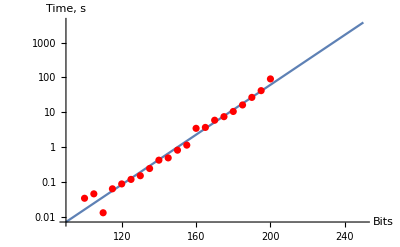

Our data contains n bits as parameter x which need to be cracked and time as parameter y. Knowing the data and exponential function we need to make the time, y logarithmic. After having treated time to logarithmic one we used the predefined function solution  = FindFit[data, a*sizeOfn+b,{a,b}, x] to find out parameter a and b. A and b is used to create our function y[sizeOfn]=ⅇ^(a *sizeOfn+b)/.solution.

We have now our model which is y[sizeOfn]=ⅇ^(a *sizeOfn+b)/.solution, where a is 0.0826339 and b equals to -12.4073. The results is then calculated by put the parameter 1024, 2048 and 4096 into the function. Which gives 7.271*10^23, 4.076*10^60 and  1.282*10^134 years respectively. The result was first in seconds and by dividing it with 60*60*24*365 which gives us the number of years it takes.

Size,bit | Time,year
1024 | 7.271*10^23
2048 | 4.076*10^60
4096 | 1.282*10^134

## Code

```mathematica
message = "DISKRET MATTE, DE E FETT NAIS!";
```

```mathematica
(* Make sure a long text break down to the size that is smaller than n *)
splitText[message_, a_, b_]:= Module[{Bytes, ascii, F, B, i, eachLineBits, case},
eachLineBits = a +b;         (* the maximum size of each line *)
Bytes = Floor[eachLineBits/8];
case = Bytes*8;
B = Which[case == eachLineBits, Bytes-1, True, Bytes];  
ascii={};
For[i=1, i <StringLength[message]/B+1, i++, 
F =Which[i*B > StringLength[message], StringLength[message], True, i*B];
AppendTo[ascii, StringTake[message,{(i-1)*B +1, F}]]
]; 
ascii
]
```

```mathematica
(* Generate the cipher with different size of n,(a+b) *)
genCipher[message_, a_, b_] := 
Module[{ pPerson, qPerson, ϕPerson,ePerson, m, nPerson, c, i, rnd, ascii},
pPerson = NextPrime[RandomInteger[{2^a, 2^a}]];
qPerson = NextPrime[RandomInteger[{2^b, 2^b}]];
ϕPerson=(pPerson-1)(qPerson-1);
nPerson = pPerson*qPerson;
rnd:=RandomInteger[{10^3,10^4}];
While[GCD[ePerson=rnd,ϕPerson]≠1];
c = splitText[message, a, b];
For [i = 1, i < Length[c]+1, i++, 
c[[i]] = ToCharacterCode[c[[i]] ]. 256^(Range[StringLength[c[[i]]]]-1);
c[[i]] = PowerMod[c[[i]] , ePerson, nPerson];
];
{nPerson, ePerson,c}       (* return n and e numbers, c is the cipher *)
]
```

```mathematica
(*Task 2*) (* function that crack the cipher to clear text *)
RSAcrack[cipher_, n_, e_] := 
Module[{t, f, pPerson, qPerson, ϕPerson, dPerson, mFromPerson, mInAscii, B, clearText, i, q, ascii,c},
{t, _G}=AbsoluteTiming[
{{pPerson,_V},{qPerson,_L}} = FactorInteger[n];
ϕPerson=(pPerson-1)(qPerson-1);
dPerson=PowerMod[e,-1,ϕPerson];
c =cipher;
For[i = 1, i <Length[cipher]+1, i++,
mFromPerson = PowerMod[cipher[[i]],dPerson,n];
q=mFromPerson;ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,256]];       
q=Quotient[q,256]
];
c[[i]] = FromCharacterCode[ascii];
];
];
clearText = StringJoin[c];
{t, clearText}     (* Return the time and clearText *)
]
```

```mathematica
(* This function repeatly create the cipher with different size and crack it *)
genData[message_, amountData_, startBit1_, startBit2_] := Module[{n, e, c, data, t, s1, s2, i, sList, tList, sTotal},
data = {};
sList = {};
tList = {};
(* each iteration increases the n with 5 bits, starting 100 and end at 200 bits *)
For[i=0, i < amountData+1, i++,  
s1=startBit1 + i*2 ;
s2 = startBit2 +i*3;
sTotal = s1 + s2;
{n,e,c} = genCipher[message, s1 , s2 ];
{t, _m} = RSAcrack[c,n,e];
temp = {(s1+s2), t};
AppendTo[data,temp];
AppendTo[sList, sTotal];
AppendTo[tList, t];
];
{data, sList, tList}     (* It gives the data(bits, x and time, y), sList(bits), tList(time) *)
]
```

```mathematica
{data, sList, tList} = genData[message, 20, 49,51]        (* generate the data to make our model *)
```

{{{100,0.0481648},{105,0.0660537},{110,0.0198386},{115,0.0873608},{120,0.128568},{125,0.16584},{130,0.213054},{135,0.326814},{140,0.558676},{145,0.664043},{150,1.13692},{155,1.54482},{160,4.68118},{165,5.11834},{170,8.07878},{175,10.3017},{180,14.2981},{185,21.903},{190,37.2677},{195,57.6007},{200,122.808}},{100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200},{0.0481648,0.0660537,0.0198386,0.0873608,0.128568,0.16584,0.213054,0.326814,0.558676,0.664043,1.13692,1.54482,4.68118,5.11834,8.07878,10.3017,14.2981,21.903,37.2677,57.6007,122.808}}

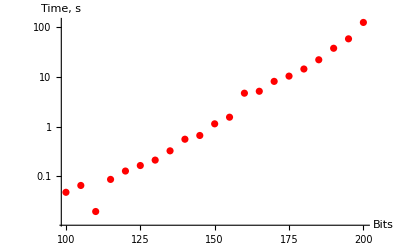

```mathematica
dataPlot = ListLogPlot[data, AxesLabel -> {"Bits", "Time, s"}, PlotStyle-> Red]
```

```mathematica
data2=Transpose[{sList,Log[tList]}];
```

```mathematica
solution=FindFit[data2,a x+b,{a,b},x](* to find out parameter a and b *)
```

{a→0.0818587,b→-11.9561}

```mathematica
y[x_]=ⅇ^(a x+b)/.solution (* this is our model *)
```

ⅇ^(-11.9561+0.0818587 x)

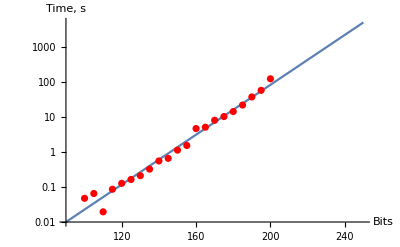

```mathematica
modelplot = LogPlot[y[x], {x,90,250}, AxesLabel -> {"Bits", "Time, s"}];
Show[modelplot, dataPlot]
```

```mathematica
secToYear = 60*60*24*365;  (* seconds in a year *)
```

```mathematica
y[1024]/secToYear
```

5.16133×10^23

```mathematica
y[2048]/secToYear
```

1.30853×10^60

```mathematica
y[4096]/ secToYear
```

8.41053×10^132